# Moments

```mathematica
SetDirectory[NotebookDirectory[]];
data=Association[];
Monitor[
Do[
data[iIC]={};
Do[
AppendTo[data[iIC],Import["../data/ic_v"<>IntegerString[iIC,10,3]<>"/lattice_v"<>IntegerString[iLatt,10,3]<>"/counts/A.txt","Table"][[;;,2]]];
,{iLatt,1,50}];
data[iIC]=Mean[data[iIC]]//N;
,{iIC,1,50}];
,ProgressIndicator[iIC,{1,50}]]
```

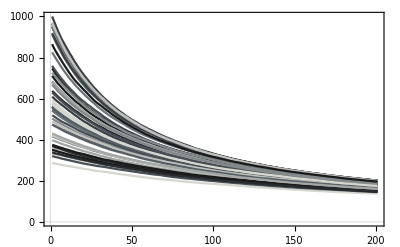

```mathematica
ListLinePlot[Values[data],PlotRange->All,PlotStyle->Map[ColorData["GrayTones"][Mod[#,10]/10.0]&,Range[1,50]]]
```

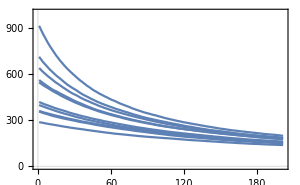

```mathematica
pltMoms=ListLinePlot[Values[data][[;;10]],PlotRange->{0,1000},PlotStyle->ColorData[97,1],ImageSize->300]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/moments.pdf",pltMoms]
```

../figures/moments.pdf